```mathematica
Import["ToMatlab.m","Package"]
```

# p=1, hexagonal flake shape, based on -Graphics-

## AA stacking Eq. 3

```mathematica
ClearAll["Global`*"]
```

```mathematica
fAA[x_,y_,λ_]=  (Cos[(4 π x)/(√3 λ)]+2 Cos[(2  π x)/(√3 λ)] Cos[(2  π y)/λ])
```

Cos[(4 π x)/(√3 λ)]+2 Cos[(2 π x)/(√3 λ)] Cos[(2 π y)/λ]

```mathematica
Plot3D[fAA[x,y,1],{x,-1,1},{y,-1,1},AxesLabel->Automatic,ViewPoint->{0,0,Infinity}, ColorFunction->"Rainbow"]
```

-Graphics3D-

```mathematica
λ0=as/(2*(1-Cos[θ]))^(1/2)
```

as/(√2 √(1-Cos[θ]))

```mathematica
f0AA[x_,y_,as_,θ_]=fAA[x,y,λ0]
```

Cos[(4 √(2/3) π x √(1-Cos[θ]))/as]+2 Cos[(2 √(2/3) π x √(1-Cos[θ]))/as] Cos[(2 √2 π y √(1-Cos[θ]))/as]

```mathematica
nRf0AA[x_,y_,as_,θ_,R_]=f0AA[x R,y R,as,θ]
```

Cos[(4 √(2/3) π R x √(1-Cos[θ]))/as]+2 Cos[(2 √(2/3) π R x √(1-Cos[θ]))/as] Cos[(2 √2 π R y √(1-Cos[θ]))/as]

```mathematica
nRnasf0AA[x_,y_,as_,θ_,r_]=nRf0AA[x,y,as,θ,r*as]
```

Cos[4 √(2/3) π r x √(1-Cos[θ])]+2 Cos[2 √(2/3) π r x √(1-Cos[θ])] Cos[2 √2 π r y √(1-Cos[θ])]

```mathematica
nRnasnareauf0AA[x_,y_,θ_,r_]=nRnasf0AA[x,y,as,θ,r]
```

Cos[4 √(2/3) π r x √(1-Cos[θ])]+2 Cos[2 √(2/3) π r x √(1-Cos[θ])] Cos[2 √2 π r y √(1-Cos[θ])]

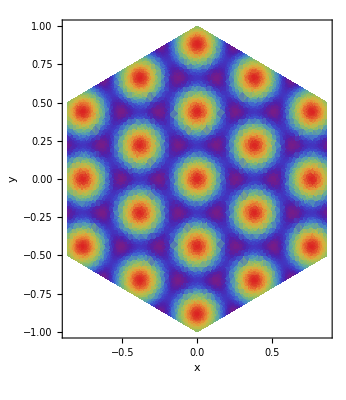

```mathematica
DensityPlot[nRnasnareauf0AA[x,y,2.5/180*Pi,30Sqrt[3]],{x,-Sqrt[3]/2,Sqrt[3]/2},{y,-1,1},AxesLabel->Automatic, ColorFunction->"Rainbow",MaxRecursion->3, PlotRange->All,RegionFunction->Function[{x,y,z},-Sqrt[3]*x/3-1<y&&y<Sqrt[3]*x/3+1&&Sqrt[3]*x/3-1<y&&y<-Sqrt[3]*x/3+1],AspectRatio->Automatic]
```

```mathematica
hexagonarea=Integrate[Boole[-Sqrt[3]*x/3-1<y&&y<Sqrt[3]*x/3+1&&Sqrt[3]*x/3-1<y&&y<-Sqrt[3]*x/3+1],{x,-Sqrt[3]/2,Sqrt[3]/2},{y,-1,1}]
```

(3 √3)/2

```mathematica
t1=AbsoluteTime[];
hexAA[θ_,r_]=FullSimplify[Integrate[nRnasnareauf0AA[x,y,θ,r]Boole[-Sqrt[3]*x/3-1<y&&y<Sqrt[3]*x/3+1&&Sqrt[3]*x/3-1<y&&y<-Sqrt[3]*x/3+1],{x,-Sqrt[3]/2,Sqrt[3]/2},{y,-1,1}]/hexagonarea]
t2=AbsoluteTime[];
Print["time used ",(t2-t1)/60," mins" ]
```

(Sin[π r √(2-2 Cos[θ])] (4 √2 π r Cos[π r √(2-2 Cos[θ])] Sin[θ/2]^2+√(1-Cos[θ]) Sin[π r √(2-2 Cos[θ])]))/(2 π^2 r^2 (1-Cos[θ])^(3/2))

time used 0.37233127 mins

```mathematica
ToMatlab[hexAA[theta,r]]
```

(1/2).*pi.^(-2).*r.^(-2).*(1+(-1).*cos(theta)).^(-3/2).*sin(pi.* ...
  r.*(2+(-2).*cos(theta)).^(1/2)).*(4.*2.^(1/2).*pi.*r.*cos(pi.*r.*( ...
  2+(-2).*cos(theta)).^(1/2)).*sin((1/2).*theta).^2+(1+(-1).*cos( ...
  theta)).^(1/2).*sin(pi.*r.*(2+(-2).*cos(theta)).^(1/2)));

## AB stacking Eq. 4

```mathematica
ClearAll["Global`*"]
```

```mathematica
fAB[x_,y_,λ_]=  (Cos[(4 π (x-λ/√3))/(√3 λ)]+2 Cos[(2  π (x-λ/√3))/(√3 λ)] Cos[(2  π y)/λ])
```

2 Cos[(2 π y)/λ] Cos[(2 π (x-λ/(√3)))/(√3 λ)]+Cos[(4 π (x-λ/(√3)))/(√3 λ)]

```mathematica
Plot3D[fAB[x,y,1],{x,-1,1},{y,-1,1},AxesLabel->Automatic,ViewPoint->{0,0,Infinity}, ColorFunction->"Rainbow"]
```

-Graphics3D-

```mathematica
λ0=as/(2*(1-Cos[θ]))^(1/2)
```

as/(√2 √(1-Cos[θ]))

```mathematica
f0AB[x_,y_,as_,θ_]=fAB[x,y,λ0]
```

2 Cos[(2 √2 π y √(1-Cos[θ]))/as] Cos[(2 √(2/3) π (x-as/(√6 √(1-Cos[θ]))) √(1-Cos[θ]))/as]+Cos[(4 √(2/3) π (x-as/(√6 √(1-Cos[θ]))) √(1-Cos[θ]))/as]

```mathematica
nRf0AB[x_,y_,as_,θ_,R_]=f0AB[x R,y R,as,θ]
```

2 Cos[(2 √2 π R y √(1-Cos[θ]))/as] Cos[(2 √(2/3) π (R x-as/(√6 √(1-Cos[θ]))) √(1-Cos[θ]))/as]+Cos[(4 √(2/3) π (R x-as/(√6 √(1-Cos[θ]))) √(1-Cos[θ]))/as]

```mathematica
nRnasf0AB[x_,y_,as_,θ_,r_]=nRf0AB[x,y,as,θ,r*as]
```

2 Cos[2 √2 π r y √(1-Cos[θ])] Cos[(2 √(2/3) π (as r x-as/(√6 √(1-Cos[θ]))) √(1-Cos[θ]))/as]+Cos[(4 √(2/3) π (as r x-as/(√6 √(1-Cos[θ]))) √(1-Cos[θ]))/as]

```mathematica
nRnasnareauf0AB[x_,y_,θ_,r_]=Simplify[nRnasf0AB[x,y,as,θ,r]]
```

Cos[4/3 π (-1+r x √(6-6 Cos[θ]))]+2 Cos[2/3 π (-1+r x √(6-6 Cos[θ]))] Cos[2 π r y √(2-2 Cos[θ])]

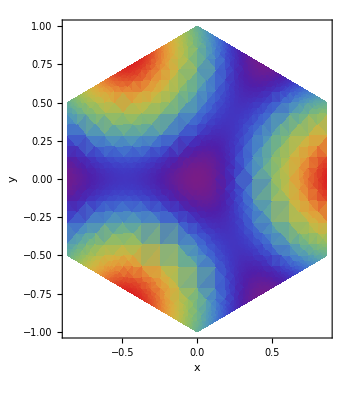

```mathematica
DensityPlot[nRnasnareauf0AB[x,y,2/180*Pi,10Sqrt[3]],{x,-Sqrt[3]/2,Sqrt[3]/2},{y,-1,1},AxesLabel->Automatic, ColorFunction->"Rainbow",MaxRecursion->3, PlotRange->All,RegionFunction->Function[{x,y,z},-Sqrt[3]*x/3-1<y&&y<Sqrt[3]*x/3+1&&Sqrt[3]*x/3-1<y&&y<-Sqrt[3]*x/3+1],AspectRatio->Automatic]
```

```mathematica
hexagonarea=Integrate[Boole[-Sqrt[3]*x/3-1<y&&y<Sqrt[3]*x/3+1&&Sqrt[3]*x/3-1<y&&y<-Sqrt[3]*x/3+1],{x,-Sqrt[3]/2,Sqrt[3]/2},{y,-1,1}]
```

(3 √3)/2

```mathematica
t3=AbsoluteTime[];
hexAB[θ_,r_]=FullSimplify[Integrate[nRnasnareauf0AB[x,y,θ,r] Boole[-Sqrt[3]*x/3-1<y&&y<Sqrt[3]*x/3+1&&Sqrt[3]*x/3-1<y&&y<-Sqrt[3]*x/3+1],{x,-Sqrt[3]/2,Sqrt[3]/2},{y,-1,1}]/hexagonarea]

t4=AbsoluteTime[];
Print["time used ",(t4-t3)/60," mins" ]
```

-(Sin[π r √(2-2 Cos[θ])] (4 √2 π r Cos[π r √(2-2 Cos[θ])] Sin[θ/2]^2+√(1-Cos[θ]) Sin[π r √(2-2 Cos[θ])]))/(4 π^2 r^2 (1-Cos[θ])^(3/2))

time used 0.610936453 mins

```mathematica
hexAB2[θ_,r_]:=(1-Cos[2 π r √(2-2 Cos[θ])]+2 π r √(2-2 Cos[θ]) Sin[2 π r √(2-2 Cos[θ])])/(8 π^2 r^2 (-1+Cos[θ]))
```

## They are the same formulas

```mathematica
Simplify[hexAB[θ,r]-hexAB2[θ,r]]
```

0

```mathematica
ToMatlab[hexAB[theta,r]]
```

(-1/4).*pi.^(-2).*r.^(-2).*(1+(-1).*cos(theta)).^(-3/2).*sin(pi.* ...
  r.*(2+(-2).*cos(theta)).^(1/2)).*(4.*2.^(1/2).*pi.*r.*cos(pi.*r.*( ...
  2+(-2).*cos(theta)).^(1/2)).*sin((1/2).*theta).^2+(1+(-1).*cos( ...
  theta)).^(1/2).*sin(pi.*r.*(2+(-2).*cos(theta)).^(1/2)));